# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["C:\\Users\\Miguel\\Github\\Entropy\\Prethermalization\\Degeneracies\\QMB_offline.wl"];
```

SetDelayed::write: Tag Commutator in Commutator[A_,B_] is Protected.

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

```mathematica
(*Clear[arrayt];
arrayt[t_,val_,vec_]:=Exp[-I*val*t]*vec;
Clear[new];
new[L_,eigenval_,eigenvec_,ini_,t_]:=Module[{schmidt,psit,ck=Conjugate[eigenvec].ini,d=2^(L/2),phases=arrayt[t,eigenval,eigenvec]},
psit=ArrayReshape[Total[N[ck*phases]],{d,d}];
Total[Map[VNentropy,(Chop[SingularValueList[psit]])^2]]];*)
```

# Test SRN

```mathematica
(*2. Parameters*)
L=8;
J=1;
g=2;
hlist=Sort[Append[Table[10^i,{i,-6,-2,0.5}],0.0]];
tlist=Developer`ToPackedArray[Table[10^i,{i,0,8,0.0005}]];
tlist//Length
hlist//Length
```

16001

10

```mathematica
states=Table[RandomChainProductState[L],{100}];
```

```mathematica
states=Table[Flatten[KroneckerProduct[haar[L/2],haar[L/2]]],{100}];
```

```mathematica
states=Table[coherentstate[qubit[Pi,Exp[-I RandomReal[]]],L],{100}];
```

```mathematica
n=Length[hlist]+1;
reds=Table[Blend[{RGBColor[0.1,0.1,1],RGBColor[1,0,0]},t],{t,1/(n-1),1,1/(n-1)}];
cf=Blend[{{0,Blue},{0.5,Purple},{1,Red}},#]&;
```

```mathematica
(*3. Build block maps and compiled fast expander*)
{evenMap,oddMap}=buildMaps[L];
ExpandFullStateFast=buildExpandFullStateFast[evenMap,oddMap,L];
```

```mathematica
(*4. Hamiltonian and evolvers*)
h=hlist[[-1]];
Ha=IsingHamiltonian[h,g,J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha,Symmetry->"Parity"];
{evenEigvals,evenEigvecs}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[1]]]]]]];
{oddEigvals,oddEigvecs}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[2]]]]]]];
evenEigvecs=Developer`ToPackedArray[evenEigvecs];
evenEigvals=Developer`ToPackedArray[evenEigvals];
oddEigvecs=Developer`ToPackedArray[oddEigvecs];
oddEigvals=Developer`ToPackedArray[oddEigvals];
evenEvolver=compiledEvolverSector[evenEigvecs,evenEigvals];
oddEvolver=compiledEvolverSector[oddEigvecs,oddEigvals];
(*5. Distribute*)
DistributeDefinitions[evenMap,oddMap,ProjectBlockVector,ExpandFullStateFast,tlist,L,new,evenEvolver,oddEvolver];
```

```mathematica
(*6. Define worker on all kernels*)
ParallelEvaluate[entanglementWorker[state_]:=Module[{psiEven,psiOdd,evenFinal,oddFinal,fullStates},{psiEven,psiOdd}={ProjectBlockVector[state,evenMap,"even",L],ProjectBlockVector[state,oddMap,"odd",L]};
evenFinal=evenEvolver[psiEven,tlist];
oddFinal=oddEvolver[psiOdd,tlist];
fullStates=Table[ExpandFullStateFast[evenFinal[[i]],oddFinal[[i]]],{i,Length[tlist]}];
Map[new[#,L]&,fullStates]];];
```

```mathematica
(*7. Run computation*)
AbsoluteTiming[data=ParallelTable[entanglementWorker[state],{state,states}];]
```

{18.9936,Null}

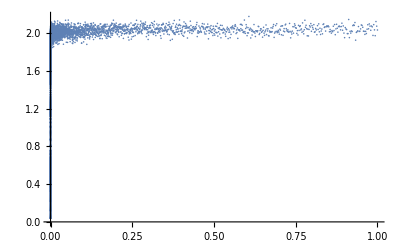

```mathematica
ListPlot[Transpose[{tlist,Mean[data]}],PlotRange->All]
```

## Exporting files

```mathematica
(* ===0) OUTPUT FOLDER+HELPERS (add this BEFORE the Do loop)===*)
outDir=FileNameJoin[{NotebookDirectory[],"SRN_entropies"}];
If[!DirectoryQ[outDir],CreateDirectory[outDir,CreateIntermediateDirectories->True]];
(*file-safe tag for h values,e.g.0.001->"h_0p001"*)
hTag[h_?NumericQ]:="h_"<>StringReplace[ToString@NumberForm[h,{Infinity,10}],{"."->"p","-"->"m"," "->""}];
(*metadata to write once at the end*)
runMeta=<|"L"->L,"J"->J,"g"->g,"hlist"->hlist,"tlist"->tlist,"NumStates"->Length[states],"TimestampStart"->DateString[{"Year","-","Month","-","Day"," ","Hour",":","Minute",":","Second"}],"WolframVersion"->$Version|>;
(*optional:keep a small per-h timing log*)
perHLog=Association[];
(*safe numeric tag for g (unchanged if you already added it)*)
gTag[x_?NumericQ]:=Module[{d=IntegerString[Floor[FractionalPart[x]*10^4+0.5],10,4]},"1p"<>d];
(*filename base using the INDEX ih,zero-padded to 2 digits*)
baseNameIdx[ih_Integer?Positive]:=StringJoin["SRN_entropies_","L",ToString[L],"_","J",ToString[J],"_","g",gTag[g],"_","h_",IntegerString[ih,10,2]  (*i01,i02,...*)];
```

```mathematica
results={};
Do[
Print["Computing for h = "<>ToString[hlist[[ih]]]];
h=hlist[[ih]];
(*Your step 4:Hamiltonian and evolvers (UNCHANGED)*)Ha=IsingHamiltonian[h,g,J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha,Symmetry->"Parity"];
{evenEigvals,evenEigvecs}=Transpose@Sort@Transpose@Quiet@Eigensystem[system[[1]]];
{oddEigvals,oddEigvecs}=Transpose@Sort@Transpose@Quiet@Eigensystem[system[[2]]];
evenEigvecs=Developer`ToPackedArray[evenEigvecs];
evenEigvals=Developer`ToPackedArray[evenEigvals];
oddEigvecs=Developer`ToPackedArray[oddEigvecs];
oddEigvals=Developer`ToPackedArray[oddEigvals];
evenEvolver=compiledEvolverSector[evenEigvecs,evenEigvals];
oddEvolver=compiledEvolverSector[oddEigvecs,oddEigvals];
(*Local (non-parallel) worker using the evolvers for THIS h—UNCHANGED*)entanglementWorker[state_]:=Module[{psiEven,psiOdd,evenFinal,oddFinal,fullStates},{psiEven,psiOdd}={ProjectBlockVector[state,evenMap,"even",L],ProjectBlockVector[state,oddMap,"odd",L]};
evenFinal=evenEvolver[psiEven,tlist];
oddFinal=oddEvolver[psiOdd,tlist];
fullStates=Table[ExpandFullStateFast[evenFinal[[i]],oddFinal[[i]]],{i,Length[tlist]}];
Map[new[#,L]&,fullStates]];
(* ===Only addition:time+export per h===*)
{dt,currentResults}=AbsoluteTiming[ParallelTable[entanglementWorker[state],{state,states}]];
AppendTo[results,currentResults];
perHLog[h]=<|"Seconds"->dt,"ResultShape"->Dimensions[currentResults]|>;
(*build trajectories:one {t,S(t)} table per state*)
trajectories=Map[Transpose[{tlist,#}]&,currentResults];
Export[FileNameJoin[{outDir,baseNameIdx[ih]<>".mx"}],trajectories,"MX"];

,{ih,Length[hlist]}];

(* ===Write metadata once at the end===*)
runMetaFinal=<|"L"->L,"J"->J,"g"->g,"hlist"->hlist,"NumStates"->Length[states],"PerHFiles"->AssociationThread[hlist,Table[baseNameIdx[i]<>".mx",{i,Length[hlist]}]]|>;
metadata=runMetaFinal;
Put[metadata,FileNameJoin[{outDir,"metadata.m"}]];
Print["Saved per-h .mx files and metadata.m to: ",outDir];
```

Computing for h = 0.0000158489

Computing for h = 0.0000251189

Computing for h = 0.0000398107

Computing for h = 0.0000630957

Computing for h = 0.0001

Computing for h = 0.000158489

Computing for h = 0.000251189

Computing for h = 0.000398107

Computing for h = 0.000630957

Computing for h = 0.001

Computing for h = 0.00158489

Computing for h = 0.00251189

Computing for h = 0.00398107

Computing for h = 0.00630957

Computing for h = 0.01

Computing for h = 0.0158489

Computing for h = 0.0251189

Computing for h = 0.0398107

Computing for h = 0.0630957

Computing for h = 0.1

Saved per-h .mx files and metadata.m to: /Users/pcs/Desktop/Entropy/Degeneracies SRN/SRN_entropies

```mathematica
data=results;
```

```mathematica
plotsa={};
Do[
ploten=Show[{ListLogLinearPlot[{Transpose[{tlist,Mean[data[[h]]]}],MovingAverage[Transpose[{tlist,Mean[data[[h]]]}],200]},PlotStyle->{Directive[Gray,Opacity[0.25]],Directive[reds[[h]],Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["SRN, OBC, Coherent states , L = "<>ToString[L]<>", J = "<>ToString[N[J]]<>", g = "<>ToString[N[g]]<>", h = "<>ToString[hlist[[h]]],35,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]}]},PlotRange->{All,{0,1}}];
AppendTo[plotsa,ploten];
,{h,Length[hlist]}];
```

```mathematica
Show[plotsa,PlotRange->All]
```

# Test LRN

```mathematica
g=1+GoldenRatio^-3;
```

```mathematica
J=1+GoldenRatio^-3./2;
```

```mathematica
(*2. Parameters*)
L=8;
J=1;
g=1+GoldenRatio^-3;
hlist=Sort[Append[Table[10^i,{i,-6,0,0.25}],0.0]];
tlist=Developer`ToPackedArray[Table[10^i,{i,5,10,0.00050}]];
tlist//Length
hlist//Length
```

10001

26

```mathematica
states=Table[RandomChainProductState[L],{100}];
```

```mathematica
states=Table[Flatten[KroneckerProduct[haar[L/2],haar[L/2]]],{100}];
```

```mathematica
n=Length[hlist]+1;
reds=Table[Blend[{RGBColor[0.1,0.1,1],RGBColor[1,0,0]},t],{t,1/(n-1),1,1/(n-1)}];
cf=Blend[{{0,Blue},{0.5,Purple},{1,Red}},#]&;
```

```mathematica
(*3. Build block maps and compiled fast expander*)
{evenMap,oddMap}=buildMaps[L];
ExpandFullStateFast=buildExpandFullStateFast[evenMap,oddMap,L];
```

```mathematica
(*4. Hamiltonian and evolvers*)
h=hlist[[-1]];
Ha=IsingHamiltonian[g,h,J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha,Symmetry->"Parity"];
{evenEigvals,evenEigvecs}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[1]]]]]]];
{oddEigvals,oddEigvecs}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[2]]]]]]];
evenEigvecs=Developer`ToPackedArray[evenEigvecs];
evenEigvals=Developer`ToPackedArray[evenEigvals];
oddEigvecs=Developer`ToPackedArray[oddEigvecs];
oddEigvals=Developer`ToPackedArray[oddEigvals];
evenEvolver=compiledEvolverSector[evenEigvecs,evenEigvals];
oddEvolver=compiledEvolverSector[oddEigvecs,oddEigvals];
(*5. Distribute*)
DistributeDefinitions[evenMap,oddMap,ProjectBlockVector,ExpandFullStateFast,tlist,L,new,evenEvolver,oddEvolver];
```

```mathematica
(*6. Define worker on all kernels*)
ParallelEvaluate[entanglementWorker[state_]:=Module[{psiEven,psiOdd,evenFinal,oddFinal,fullStates},{psiEven,psiOdd}={ProjectBlockVector[state,evenMap,"even",L],ProjectBlockVector[state,oddMap,"odd",L]};
evenFinal=evenEvolver[psiEven,tlist];
oddFinal=oddEvolver[psiOdd,tlist];
fullStates=Table[ExpandFullStateFast[evenFinal[[i]],oddFinal[[i]]],{i,Length[tlist]}];
Map[new[#,L]&,fullStates]];];
```

```mathematica
(*7. Run computation*)
AbsoluteTiming[data=ParallelTable[entanglementWorker[state],{state,states}];]
```

{19.5737,Null}

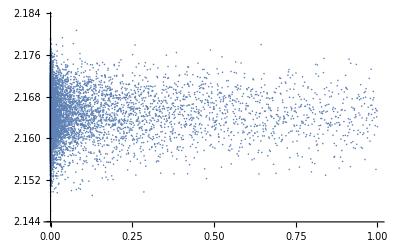

```mathematica
ListPlot[Transpose[{tlist,Mean[data]}],PlotRange->All]
```

## Exporting files

```mathematica
(* ===0) OUTPUT FOLDER+HELPERS (add this BEFORE the Do loop)===*)
outDir=FileNameJoin[{NotebookDirectory[],"LRN_entropies"}];
If[!DirectoryQ[outDir],CreateDirectory[outDir,CreateIntermediateDirectories->True]];
(*file-safe tag for h values,e.g.0.001->"h_0p001"*)
hTag[h_?NumericQ]:="h_"<>StringReplace[ToString@NumberForm[h,{Infinity,10}],{"."->"p","-"->"m"," "->""}];
(*metadata to write once at the end*)
runMeta=<|"L"->L,"J"->J,"g"->g,"hlist"->hlist,"tlist"->tlist,"NumStates"->Length[states],"TimestampStart"->DateString[{"Year","-","Month","-","Day"," ","Hour",":","Minute",":","Second"}],"WolframVersion"->$Version|>;
(*optional:keep a small per-h timing log*)
perHLog=Association[];
(*safe numeric tag for g (unchanged if you already added it)*)
gTag[x_?NumericQ]:=Module[{d=IntegerString[Floor[FractionalPart[x]*10^4+0.5],10,4]},"1p"<>d];
(*filename base using the INDEX ih,zero-padded to 2 digits*)
baseNameIdx[ih_Integer?Positive]:=StringJoin["LRN_entropies_","L",ToString[L],"_","J",ToString[J],"_","g",gTag[g],"_","h_",IntegerString[ih,10,2]  (*i01,i02,...*)];
```

```mathematica
results={};
Do[
Print["Computing for h = "<>ToString[hlist[[ih]]]];
h=hlist[[ih]];
(*Your step 4:Hamiltonian and evolvers (UNCHANGED)*)Ha=IsingHamiltonian[g,h,J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha,Symmetry->"Parity"];
{evenEigvals,evenEigvecs}=Transpose@Sort@Transpose@Quiet@Eigensystem[system[[1]]];
{oddEigvals,oddEigvecs}=Transpose@Sort@Transpose@Quiet@Eigensystem[system[[2]]];
evenEigvecs=Developer`ToPackedArray[evenEigvecs];
evenEigvals=Developer`ToPackedArray[evenEigvals];
oddEigvecs=Developer`ToPackedArray[oddEigvecs];
oddEigvals=Developer`ToPackedArray[oddEigvals];
evenEvolver=compiledEvolverSector[evenEigvecs,evenEigvals];
oddEvolver=compiledEvolverSector[oddEigvecs,oddEigvals];
(*Local (non-parallel) worker using the evolvers for THIS h—UNCHANGED*)entanglementWorker[state_]:=Module[{psiEven,psiOdd,evenFinal,oddFinal,fullStates},{psiEven,psiOdd}={ProjectBlockVector[state,evenMap,"even",L],ProjectBlockVector[state,oddMap,"odd",L]};
evenFinal=evenEvolver[psiEven,tlist];
oddFinal=oddEvolver[psiOdd,tlist];
fullStates=Table[ExpandFullStateFast[evenFinal[[i]],oddFinal[[i]]],{i,Length[tlist]}];
Map[new[#,L]&,fullStates]];
(* ===Only addition:time+export per h===*)
{dt,currentResults}=AbsoluteTiming[ParallelTable[entanglementWorker[state],{state,states}]];
AppendTo[results,currentResults];
perHLog[h]=<|"Seconds"->dt,"ResultShape"->Dimensions[currentResults]|>;
(*build trajectories:one {t,S(t)} table per state*)
trajectories=Map[Transpose[{tlist,#}]&,currentResults];
Export[FileNameJoin[{outDir,baseNameIdx[ih]<>".mx"}],trajectories,"MX"];

,{ih,Length[hlist]}];

(* ===Write metadata once at the end===*)
runMetaFinal=<|"L"->L,"J"->J,"g"->g,"hlist"->hlist,"NumStates"->Length[states],"PerHFiles"->AssociationThread[hlist,Table[baseNameIdx[i]<>".mx",{i,Length[hlist]}]]|>;
metadata=runMetaFinal;
Put[metadata,FileNameJoin[{outDir,"metadata.m"}]];
Print["Saved per-h .mx files and metadata.m to: ",outDir];
```

Computing for h =           -6
1.77828 10

Computing for h =           -6
3.16228 10

Computing for h =           -6
5.62341 10

Computing for h = 0.00001

Computing for h = 0.0000177828

Computing for h = 0.0000316228

Computing for h = 0.0000562341

Computing for h = 0.0001

Computing for h = 0.000177828

Computing for h = 0.000316228

Computing for h = 0.000562341

Computing for h = 0.001

Computing for h = 0.00177828

Computing for h = 0.00316228

Computing for h = 0.00562341

Computing for h = 0.01

Computing for h = 0.0177828

Computing for h = 0.0316228

Computing for h = 0.0562341

Computing for h = 0.1

Computing for h = 0.177828

Computing for h = 0.316228

Computing for h = 0.562341

Computing for h = 1.

Saved per-h .mx files and metadata.m to: /Users/pcs/Desktop/Entropy/Degeneracies SRN/LRN_entropies

```mathematica
data=results;
```

```mathematica
plotsa={};
Do[
ploten=Show[{ListLogLinearPlot[{Transpose[{tlist,Mean[data[[h]]]}],MovingAverage[Transpose[{tlist,Mean[data[[h]]]}],200]},PlotStyle->{Directive[Gray,Opacity[0.25]],Directive[reds[[h]],Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[N[J]]<>", h = "<>ToString[N[g]],35,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]}]},PlotRange->{All,{0,1}}];
AppendTo[plotsa,ploten];
,{h,Length[hlist]}];
```

```mathematica
Show[plotsa,PlotRange->All]
```

# Degeneracies LRN

```mathematica
L=8;
J=1;
```

```mathematica
visited=ConstantArray[False,2^L,SparseArray];
evenMap={};
oddMap={};
Do[
If[!visited[[i+1]],
j=revIndex[i,L];
visited[[i+1]]=True;
visited[[j+1]]=True;
If[i==j,AppendTo[evenMap,{i}],AppendTo[evenMap,{i,j}];
AppendTo[oddMap,{i,j}];
];]
,{i,0,(2^L)-1}];
```

```mathematica
hz=0.;
levels={};
Do[
Ha=-IsingHamiltonian[hx,hz,J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha, Symmetry->"Parity"];
eveneigenval=Quiet[Eigenvalues[system[[1]]]];
oddeigenval=Quiet[Eigenvalues[system[[2]]]];
speca=Sort[Join[eveneigenval,oddeigenval]];
AppendTo[levels,Transpose[{ConstantArray[hx,2^L],Sort[Join[eveneigenval,oddeigenval]]}]]
,{hx,0,2,0.0025}];
```

```mathematica
xs={0.1,0.3,1.0};
```

```mathematica
plot=ListPlot[Flatten[levels,1],PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,30],PlotLabel->Style["LRN, L = "<>ToString[L]<>", J = "<>ToString[J]<>", g = 0",35,Black],FrameLabel->{Style["h",35,Black],Rotate[Style["E",35,Black],-90Degree]},GridLines->None,PlotRange->All,ImageSize->1000,AspectRatio->0.6,Epilog->{Directive[Red,Dashed,Thick],Table[InfiniteLine[{{x,0},{x,1}}],{x,xs}]}]
Export["LRN_levels.png",plot];
```

-Graphics-

```mathematica
hx=1.;
levels={};
Do[
Ha=-IsingHamiltonian[hx,10^hz,J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha, Symmetry->"Parity"];
eveneigenval=Quiet[Eigenvalues[system[[1]]]];
oddeigenval=Quiet[Eigenvalues[system[[2]]]];
speca=Sort[Join[eveneigenval,oddeigenval]];
AppendTo[levels,Transpose[{ConstantArray[10^hz,2^L],Sort[Join[eveneigenval,oddeigenval]]}]]
,{hz,-8,-1,0.02}];
```

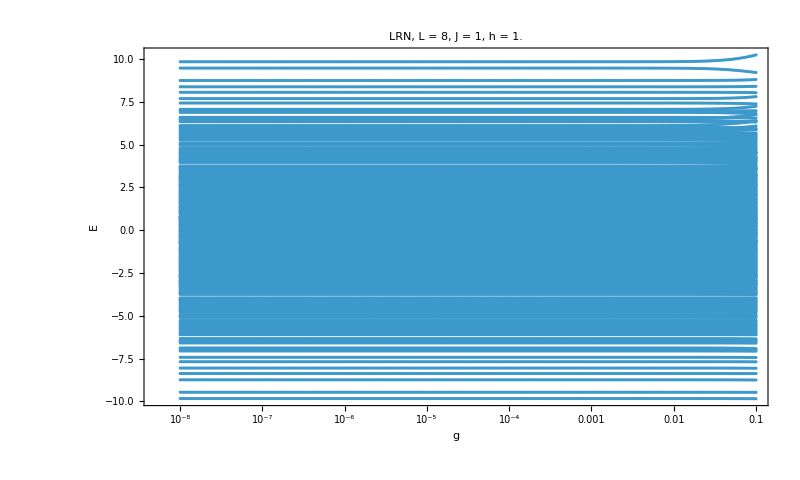

```mathematica
plot=ListLogLinearPlot[Flatten[levels,1],PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[hx],35,Black],FrameLabel->{Style["g",25,Black],Rotate[Style["E",25,Black],-90 Degree]},FrameTicks->{Automatic,{Table[{10^i,Superscript[10,i]},{i,-8,-1}],None}},GridLines->None,PlotRange->All,ImageSize->800,AspectRatio->0.6]
Export["LRN_levels_hx_"<>ToString[hx]<>"_.png",plot];
```

## level density

```mathematica
levels//Dimensions
```

{1501,256,2}

```mathematica
data=Flatten[levels,1];
```

```mathematica
data//Dimensions
```

{384256,2}

```mathematica
data[[1;;5]]
```

{{0.,-7.},{0.,-7.},{0.,-5.},{0.,-5.},{0.,-5.}}

```mathematica
data[[-5;;-1]]
```

{{3.,21.},{3.,21.},{3.,23.},{3.,23.},{3.,31.}}

```mathematica
Clear[ClusterEnergiesAtLambda];
ClusterEnergiesAtLambda[energies_List,δ_?NumericQ]:=Module[{sorted,clusters},sorted=Sort[energies];
clusters=Split[sorted,#2-#1<=δ&];
clusters];
```

```mathematica
(*parameter values:one λ per block of 256 levels*)
lamVals=levels[[All,1,1]];
(*eigenvalues:for each λ,the 256 energies*)
eigVals=levels[[All,All,2]];
(*quick sanity check on shapes*)
{Dimensions[lamVals],Dimensions[eigVals]}
```

{{1501},{1501,256}}

```mathematica
(*choose a first guess for the degeneracy tolerance*)
deltaE=10.^-3;  (*you can later tune this value*)
(*pick one parameter index to test,e.g.the first one*)
i0=1;
(*compute clusters of almost-degenerate energies at this λ*)
testClusters=ClusterEnergiesAtLambda[eigVals[[i0]],deltaE];
(*sanity check:total number of energies in all clusters should be 256*)
{Length[eigVals[[i0]]],Total[Length/@testClusters]}
```

{256,256}

```mathematica
Clear[ClusterSummaryAtIndex];
ClusterSummaryAtIndex[i_Integer]:=Module[{λ,clusters,means,degeneracies},λ=lamVals[[i]];
clusters=ClusterEnergiesAtLambda[eigVals[[i]],deltaE];
means=Mean/@clusters;
degeneracies=Length/@clusters;
Transpose[{ConstantArray[λ,Length[clusters]],means,degeneracies}]];
```

```mathematica
testSummary=ClusterSummaryAtIndex[i0];
{Dimensions[testSummary],testSummary[[1;;Min[5,Length[testSummary]]]]}
```

{{8,3},{{0.,-7.,2},{0.,-5.,14},{0.,-3.,42},{0.,-1.,70},{0.,1.,70}}}

```mathematica
clusterDataByLam=ClusterSummaryAtIndex/@Range[Length[lamVals]];
clusterData=Flatten[clusterDataByLam,1];
{Dimensions[clusterData],clusterData[[1;;5]]}
```

{{49400,3},{{0.,-7.,2},{0.,-5.,14},{0.,-3.,42},{0.,-1.,70},{0.,1.,70}}}

```mathematica
degMinMax={Min[clusterData[[All,3]]],Max[clusterData[[All,3]]]}
```

{1,70}

```mathematica
degToColor[g_]:=ColorData["Rainbow"][Rescale[g,{1,256}]];
degToSize[g_]:=Rescale[g,{1,70},{0.003,0.02}];

testDegs={1,2,10,30,70};
{degToColor/@testDegs,degToSize/@testDegs}
```

{{RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.4613506980392157, 0.10931903529411766, 0.5356405019607844],RGBColor[0.38086028235294117, 0.11374331764705883, 0.6046365176470588],RGBColor[0.2616114196078431, 0.2059386431372549, 0.7502680078431372],RGBColor[0.2792316, 0.5192464470588235, 0.7818211882352941]},{0.003,0.00324638,0.00521739,0.0101449,0.02}}

# Degeneracies SRN

```mathematica
L=8;
J=1;
```

```mathematica
visited=ConstantArray[False,2^L,SparseArray];
evenMap={};
oddMap={};
Do[
If[!visited[[i+1]],
j=revIndex[i,L];
visited[[i+1]]=True;
visited[[j+1]]=True;
If[i==j,AppendTo[evenMap,{i}],AppendTo[evenMap,{i,j}];
AppendTo[oddMap,{i,j}];
];]
,{i,0,(2^L)-1}];
```

```mathematica
hx=0.;
levels={};
Do[
Ha=-IsingHamiltonian[hx,hz,J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha, Symmetry->"Parity"];
eveneigenval=Quiet[Eigenvalues[system[[1]]]];
oddeigenval=Quiet[Eigenvalues[system[[2]]]];
speca=Sort[Join[eveneigenval,oddeigenval]];
AppendTo[levels,Transpose[{ConstantArray[hz,2^L],Sort[Join[eveneigenval,oddeigenval]]}]]
,{hz,0,3,0.0025}];
```

```mathematica
xs={1.,2.};
```

```mathematica
plot=ListPlot[Flatten[levels,1],PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,30],PlotLabel->Style["SRN, L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 0",35,Black],FrameLabel->{Style["g",35,Black],Rotate[Style["E",35,Black],-90Degree]},GridLines->None,PlotRange->All,ImageSize->1000,AspectRatio->0.6,Epilog->{Directive[Red,Dashed,Thick],Table[InfiniteLine[{{x,0},{x,1}}],{x,xs}]},Background->White]
Export["SRN_levels.png",plot];
```

-Graphics-

```mathematica
hz=1.;
levels={};
Do[
Ha=-IsingHamiltonian[10^hx,hz,J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha, Symmetry->"Parity"];
eveneigenval=Quiet[Eigenvalues[system[[1]]]];
oddeigenval=Quiet[Eigenvalues[system[[2]]]];
speca=Sort[Join[eveneigenval,oddeigenval]];
AppendTo[levels,Transpose[{ConstantArray[10^hx,2^L],Sort[Join[eveneigenval,oddeigenval]]}]]
,{hx,-8,-1,0.02}];
```

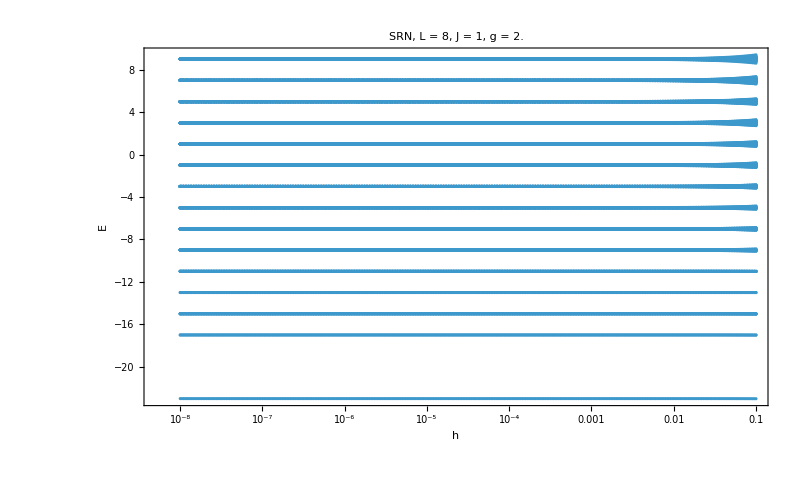

```mathematica
plot=ListLogLinearPlot[Flatten[levels,1],PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["SRN, L = "<>ToString[L]<>", J = "<>ToString[J]<>", g = "<>ToString[hz],35,Black],FrameLabel->{Style["h",25,Black],Rotate[Style["E",25,Black],-90 Degree]},FrameTicks->{Automatic,{Table[{10^i,Superscript[10,i]},{i,-8,-1}],None}},GridLines->None,PlotRange->All,ImageSize->800,AspectRatio->0.6]
Export["SRN_levels_hz_"<>ToString[hz]<>"_.png",plot];
```

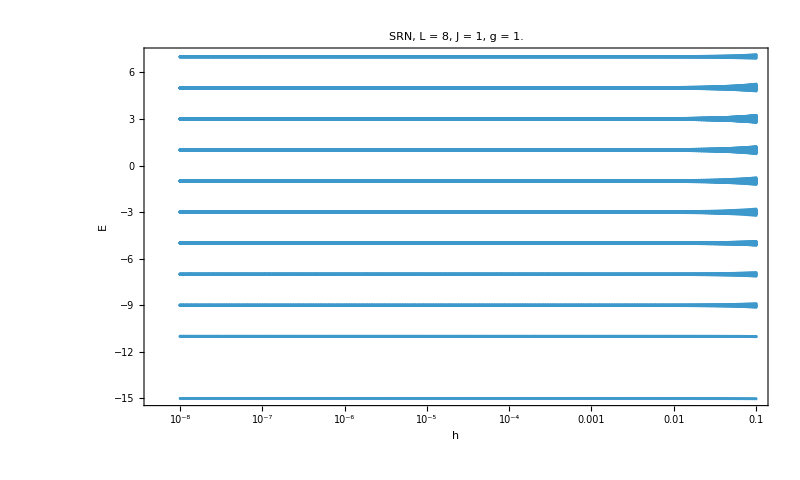

```mathematica
plot=ListLogLinearPlot[Flatten[levels,1],PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["SRN, L = "<>ToString[L]<>", J = "<>ToString[J]<>", g = "<>ToString[hz],35,Black],FrameLabel->{Style["h",25,Black],Rotate[Style["E",25,Black],-90 Degree]},FrameTicks->{Automatic,{Table[{10^i,Superscript[10,i]},{i,-8,-1}],None}},GridLines->None,PlotRange->All,ImageSize->800,AspectRatio->0.6]
Export["SRN_levels_hz_"<>ToString[hz]<>"_.png",plot];
```

## level density

```mathematica
levels//Dimensions
```

{1501,256,2}

```mathematica
data=Flatten[levels,1];
```

```mathematica
data//Dimensions
```

{384256,2}

```mathematica
data[[1;;5]]
```

{{0.,-7.},{0.,-7.},{0.,-5.},{0.,-5.},{0.,-5.}}

```mathematica
data[[-5;;-1]]
```

{{3.,21.},{3.,21.},{3.,23.},{3.,23.},{3.,31.}}

```mathematica
Clear[ClusterEnergiesAtLambda];
ClusterEnergiesAtLambda[energies_List,δ_?NumericQ]:=Module[{sorted,clusters},sorted=Sort[energies];
clusters=Split[sorted,#2-#1<=δ&];
clusters];
```

```mathematica
(*parameter values:one λ per block of 256 levels*)
lamVals=levels[[All,1,1]];
(*eigenvalues:for each λ,the 256 energies*)
eigVals=levels[[All,All,2]];
(*quick sanity check on shapes*)
{Dimensions[lamVals],Dimensions[eigVals]}
```

{{1501},{1501,256}}

```mathematica
(*choose a first guess for the degeneracy tolerance*)
deltaE=10.^-3;  (*you can later tune this value*)
(*pick one parameter index to test,e.g.the first one*)
i0=1;
(*compute clusters of almost-degenerate energies at this λ*)
testClusters=ClusterEnergiesAtLambda[eigVals[[i0]],deltaE];
(*sanity check:total number of energies in all clusters should be 256*)
{Length[eigVals[[i0]]],Total[Length/@testClusters]}
```

{256,256}

```mathematica
Clear[ClusterSummaryAtIndex];
ClusterSummaryAtIndex[i_Integer]:=Module[{λ,clusters,means,degeneracies},λ=lamVals[[i]];
clusters=ClusterEnergiesAtLambda[eigVals[[i]],deltaE];
means=Mean/@clusters;
degeneracies=Length/@clusters;
Transpose[{ConstantArray[λ,Length[clusters]],means,degeneracies}]];
```

```mathematica
testSummary=ClusterSummaryAtIndex[i0];
{Dimensions[testSummary],testSummary[[1;;Min[5,Length[testSummary]]]]}
```

{{8,3},{{0.,-7.,2},{0.,-5.,14},{0.,-3.,42},{0.,-1.,70},{0.,1.,70}}}

```mathematica
clusterDataByLam=ClusterSummaryAtIndex/@Range[Length[lamVals]];
clusterData=Flatten[clusterDataByLam,1];
{Dimensions[clusterData],clusterData[[1;;5]]}
```

{{49400,3},{{0.,-7.,2},{0.,-5.,14},{0.,-3.,42},{0.,-1.,70},{0.,1.,70}}}

```mathematica
degMinMax={Min[clusterData[[All,3]]],Max[clusterData[[All,3]]]}
```

{1,70}

```mathematica
degToColor[g_]:=ColorData["Rainbow"][Rescale[g,{1,256}]];
degToSize[g_]:=Rescale[g,{1,70},{0.003,0.02}];

testDegs={1,2,10,30,70};
{degToColor/@testDegs,degToSize/@testDegs}
```

{{RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.4613506980392157, 0.10931903529411766, 0.5356405019607844],RGBColor[0.38086028235294117, 0.11374331764705883, 0.6046365176470588],RGBColor[0.2616114196078431, 0.2059386431372549, 0.7502680078431372],RGBColor[0.2792316, 0.5192464470588235, 0.7818211882352941]},{0.003,0.00324638,0.00521739,0.0101449,0.02}}

# Test SRN single state

```mathematica
(*2. Parameters*)
L=8;
J=1;
g=1.;
hlist=Sort[Append[Table[10^i,{i,-8,0,0.5}],0.0]];
hlist//Length
```

18

```mathematica
(*states=Table[RandomChainProductState[L],{100}];
states=Table[coherentstate[qubit[Pi,Exp[-I RandomReal[]]],L],{100}];*)
```

```mathematica
states=Table[Flatten[KroneckerProduct[haar[L/2],haar[L/2]]],{10}];
```

```mathematica
n=Length[hlist]+1;
reds=Table[Blend[{RGBColor[0.1,0.1,1],RGBColor[1,0,0]},t],{t,1/(n-1),1,1/(n-1)}];
cf=Blend[{{0,Blue},{0.5,Purple},{1,Red}},#]&;
```

```mathematica
(*3. Build block maps and compiled fast expander*)
{evenMap,oddMap}=buildMaps[L];
ExpandFullStateFast=buildExpandFullStateFast[evenMap,oddMap,L];
```

```mathematica
tlist=Developer`ToPackedArray[Table[i,{i,0.1,10000,0.1}]];
tlist//Length
```

100000

```mathematica
tlist=Developer`ToPackedArray[Table[10^i,{i,-1,10,0.002}]];
tlist//Length
```

5501

```mathematica
Do[
(*4. Hamiltonian and evolvers*)
Ha=IsingHamiltonian[0.1,hlist[[h]],J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha,Symmetry->"Parity"];
{evenEigvals,evenEigvecs}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[1]]]]]]];
{oddEigvals,oddEigvecs}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[2]]]]]]];
evenEigvecs=Developer`ToPackedArray[evenEigvecs];
evenEigvals=Developer`ToPackedArray[evenEigvals];
oddEigvecs=Developer`ToPackedArray[oddEigvecs];
oddEigvals=Developer`ToPackedArray[oddEigvals];
evenEvolver=compiledEvolverSector[evenEigvecs,evenEigvals];
oddEvolver=compiledEvolverSector[oddEigvecs,oddEigvals];
(*5. Distribute*)
DistributeDefinitions[evenMap,oddMap,ProjectBlockVector,ExpandFullStateFast,tlist,L,new,evenEvolver,oddEvolver];
(*6. Define worker on all kernels*)
ParallelEvaluate[entanglementWorker[state_]:=Module[{psiEven,psiOdd,evenFinal,oddFinal,fullStates},{psiEven,psiOdd}={ProjectBlockVector[state,evenMap,"even",L],ProjectBlockVector[state,oddMap,"odd",L]};
evenFinal=evenEvolver[psiEven,tlist];
oddFinal=oddEvolver[psiOdd,tlist];
fullStates=Table[ExpandFullStateFast[evenFinal[[i]],oddFinal[[i]]],{i,Length[tlist]}];
Map[new[#,L]&,fullStates]];];
(*7. Run computation*)
(*AbsoluteTiming[data=ParallelTable[entanglementWorker[state],{state,states}];];*)
data=ParallelTable[entanglementWorker[state],{state,states}];
plot3=ListPlot[Transpose[{tlist,data[[1]]}],FrameStyle->Directive[Black,20],PlotLabel->Style["SRN, OBC, Haar , L = "<>ToString[L]<>", J = "<>ToString[N[J]]<>", g = "<>ToString[N[g]]<>", h = "<>ToString[N[hlist[[h]]]],25,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]},LabelStyle->Directive[Black,18],ImageSize->600];
fft=Fourier[data[[1]],FourierParameters->{-1,1}];
n=Length[data[[1]]];
dt=tlist[[2]]-tlist[[1]];          (*should be constant*)
freqList=Range[0,n-1]/(n*dt);    (*cycles per time unit*)
omegaList=2 Pi freqList;             (*angular frequencies*)
fftShifted=RotateRight[fft,Floor[n/2]];
omegaShifted=omegaList-omegaList[[Floor[n/2]+1]];
plot1=ListLogLogPlot[Transpose[{omegaList[[1;;Floor[n/2]]],Abs[fft][[1;;Floor[n/2]]]}],AxesLabel->{"ω","|S̃_A(ω)|"},LabelStyle->Directive[Black,18],PlotLabel->Style["SRN, OBC, Haar , L = "<>ToString[L]<>", J = "<>ToString[N[J]]<>", g = "<>ToString[N[g]]<>", h = "<>ToString[N[hlist[[h]]]],25,Black],PlotRange->All,ImageSize->600];
plot2=Periodogram[data[[1]],FrameStyle->Directive[Black,20],PlotLabel->Style["SRN, OBC, Haar , L = "<>ToString[L]<>", J = "<>ToString[N[J]]<>", g = "<>ToString[N[g]]<>", h = "<>ToString[N[hlist[[h]]]],25,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]},LabelStyle->Directive[Black,18],ImageSize->600];
Export["plot1b_h_"<>ToString[N[h]]<>"_.png",plot1];
Export["plot2b_h_"<>ToString[N[h]]<>"_.png",plot2];
Export["plot3b_h_"<>ToString[N[h]]<>"_.png",plot3];
,{h,Length[hlist]}]
```

$Aborted

## Exporting files

```mathematica
(*2. Parameters*)
L=8;
J=1;
g=2.0;
hlist=Sort[Append[Table[10^i,{i,-8,-1,0.5}],0.0]];
hlist//Length
```

16

```mathematica
(* ===0) OUTPUT FOLDER+HELPERS (add this BEFORE the Do loop)===*)
outDir=FileNameJoin[{NotebookDirectory[],"SRN_entropies"}];
If[!DirectoryQ[outDir],CreateDirectory[outDir,CreateIntermediateDirectories->True]];
(*file-safe tag for h values,e.g.0.001->"h_0p001"*)
hTag[h_?NumericQ]:="h_"<>StringReplace[ToString@NumberForm[h,{Infinity,10}],{"."->"p","-"->"m"," "->""}];
(*metadata to write once at the end*)
runMeta=<|"L"->L,"J"->J,"g"->g,"hlist"->hlist,"tlist"->tlist,"NumStates"->Length[states],"TimestampStart"->DateString[{"Year","-","Month","-","Day"," ","Hour",":","Minute",":","Second"}],"WolframVersion"->$Version|>;
(*optional:keep a small per-h timing log*)
perHLog=Association[];
(*safe numeric tag for g (unchanged if you already added it)*)
gTag[x_?NumericQ]:=Module[{d=IntegerString[Floor[FractionalPart[x]*10^4+0.5],10,4]},"1p"<>d];
(*filename base using the INDEX ih,zero-padded to 2 digits*)
baseNameIdx[ih_Integer?Positive]:=StringJoin["SRN_entropies_","L",ToString[L],"_","J",ToString[J],"_","g",gTag[g],"_","h_",IntegerString[ih,10,2]  (*i01,i02,...*)];
```

```mathematica
results={};
Do[
Print["Computing for h = "<>ToString[hlist[[ih]]]];
h=hlist[[ih]];
(*Your step 4:Hamiltonian and evolvers (UNCHANGED)*)Ha=IsingHamiltonian[h,g,J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha,Symmetry->"Parity"];
{evenEigvals,evenEigvecs}=Transpose@Sort@Transpose@Quiet@Eigensystem[system[[1]]];
{oddEigvals,oddEigvecs}=Transpose@Sort@Transpose@Quiet@Eigensystem[system[[2]]];
evenEigvecs=Developer`ToPackedArray[evenEigvecs];
evenEigvals=Developer`ToPackedArray[evenEigvals];
oddEigvecs=Developer`ToPackedArray[oddEigvecs];
oddEigvals=Developer`ToPackedArray[oddEigvals];
evenEvolver=compiledEvolverSector[evenEigvecs,evenEigvals];
oddEvolver=compiledEvolverSector[oddEigvecs,oddEigvals];
(*Local (non-parallel) worker using the evolvers for THIS h—UNCHANGED*)entanglementWorker[state_]:=Module[{psiEven,psiOdd,evenFinal,oddFinal,fullStates},{psiEven,psiOdd}={ProjectBlockVector[state,evenMap,"even",L],ProjectBlockVector[state,oddMap,"odd",L]};
evenFinal=evenEvolver[psiEven,tlist];
oddFinal=oddEvolver[psiOdd,tlist];
fullStates=Table[ExpandFullStateFast[evenFinal[[i]],oddFinal[[i]]],{i,Length[tlist]}];
Map[new[#,L]&,fullStates]];
(* ===Only addition:time+export per h===*)
{dt,currentResults}=AbsoluteTiming[ParallelTable[entanglementWorker[state],{state,states}]];
AppendTo[results,currentResults];
perHLog[h]=<|"Seconds"->dt,"ResultShape"->Dimensions[currentResults]|>;
(*build trajectories:one {t,S(t)} table per state*)
trajectories=Map[Transpose[{tlist,#}]&,currentResults];
Export[FileNameJoin[{outDir,baseNameIdx[ih]<>".mx"}],trajectories,"MX"];

,{ih,Length[hlist]}];

(* ===Write metadata once at the end===*)
runMetaFinal=<|"L"->L,"J"->J,"g"->g,"hlist"->hlist,"NumStates"->Length[states],"PerHFiles"->AssociationThread[hlist,Table[baseNameIdx[i]<>".mx",{i,Length[hlist]}]]|>;
metadata=runMetaFinal;
Put[metadata,FileNameJoin[{outDir,"metadata.m"}]];
Print["Saved per-h .mx files and metadata.m to: ",outDir];
```

```mathematica
data=results;
```

```mathematica
plotsa={};
Do[
ploten=Show[{ListLogLinearPlot[{Transpose[{tlist,data[[h,2]]}],MovingAverage[Transpose[{tlist,data[[h,2]]}],200]},PlotStyle->{Directive[Gray,Opacity[0.25]],Directive[reds[[h]],Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["SRN, OBC, Haar , L = "<>ToString[L]<>", J = "<>ToString[N[J]]<>", g = "<>ToString[N[g]],35,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]}]},PlotRange->{All,{0,1}}];
AppendTo[plotsa,ploten];
,{h,Length[hlist]}];
```

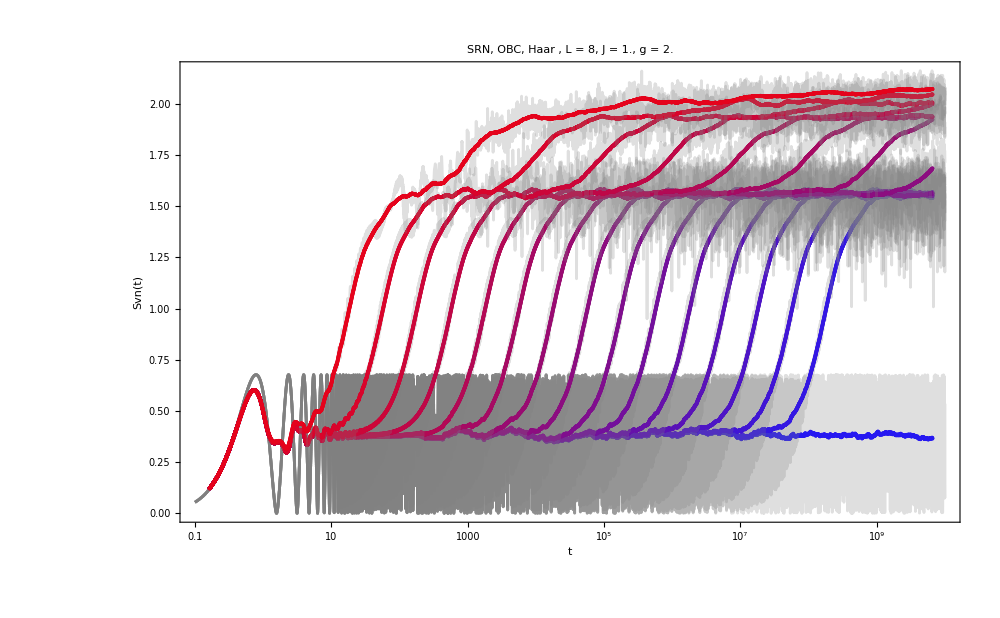

```mathematica
Show[plotsa,PlotRange->All]
```

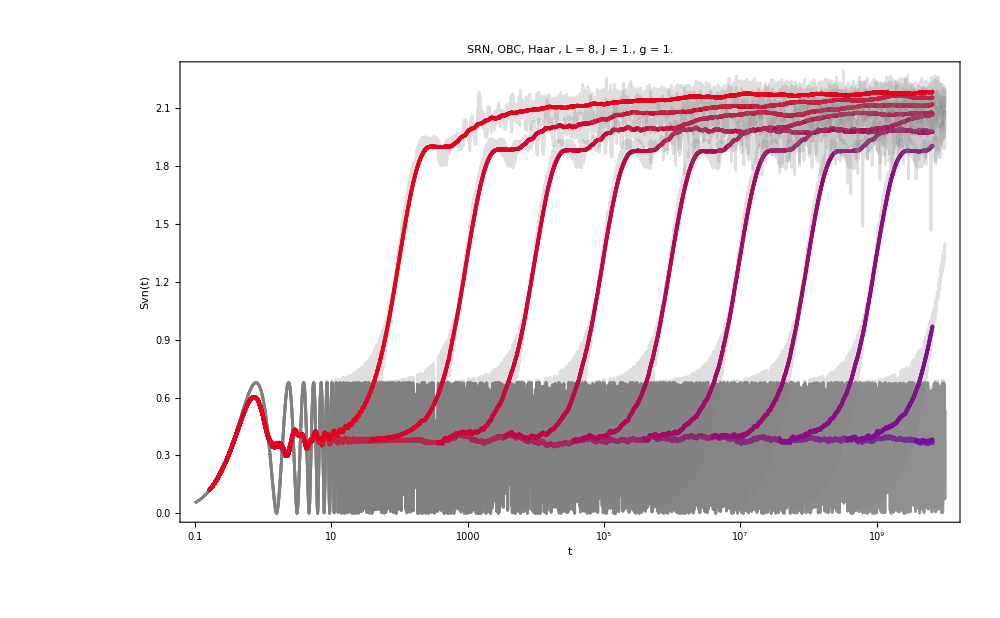

```mathematica
Show[plotsa,PlotRange->All]
```

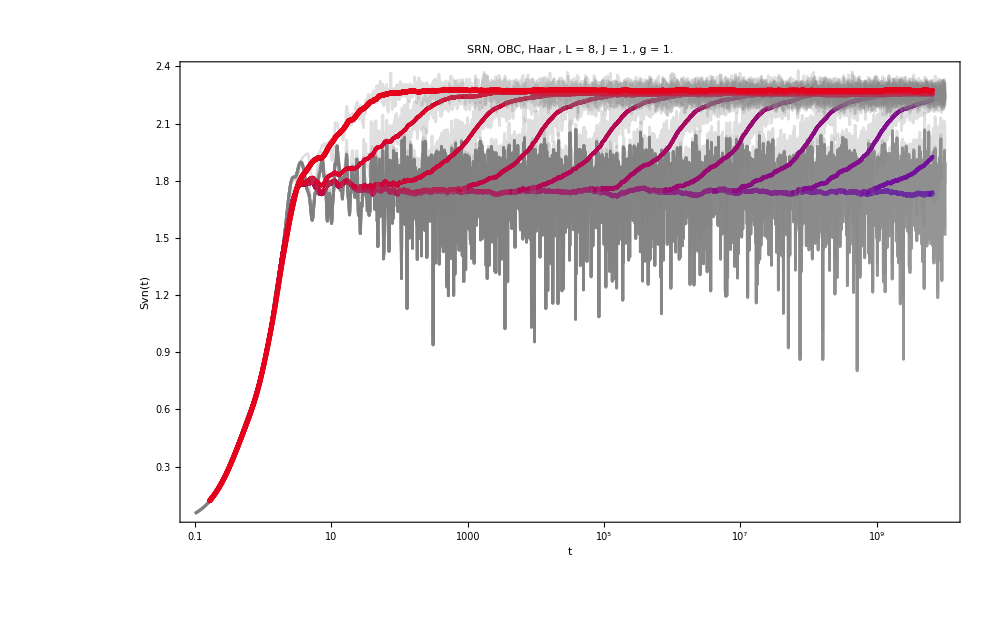

```mathematica
Show[plotsa,PlotRange->All]
```

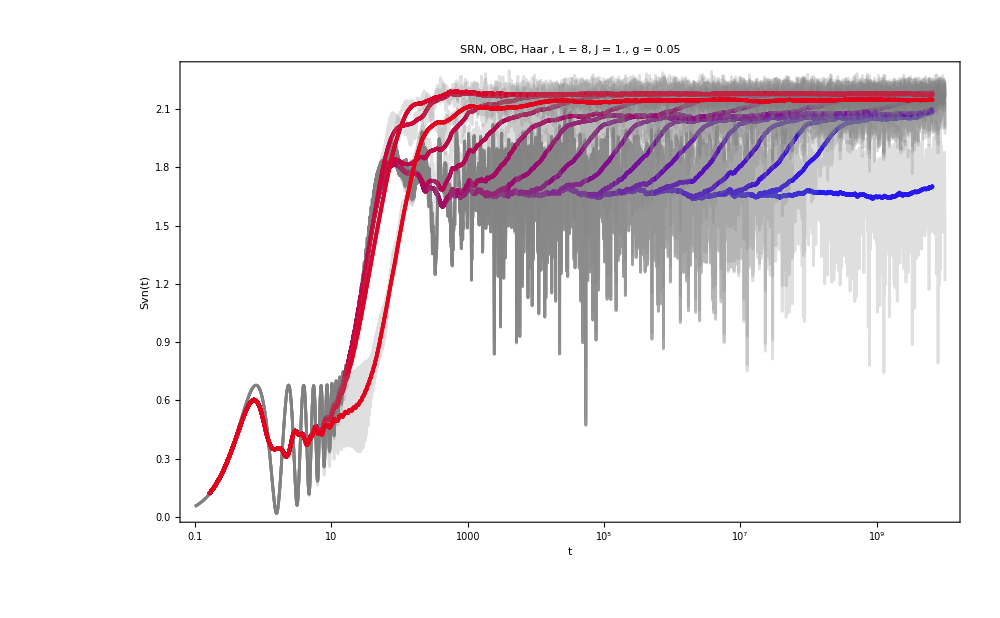

```mathematica
Show[plotsa,PlotRange->All]
```

```mathematica
Show[plotsa,PlotRange->All]
```

-Graphics-